```mathematica
loadNotebook["inz_off_6_model.nb"];
```

```mathematica
wyliczSterowanie[wd_,w_,k1_,k2_]:=(
vtotheta[xp_,yp_] := ArcSin[trim[(1/(0.03*wirowanie))*(-yp),-0.99, 0.99]];
vtophi[xp_,yp_] :=ArcSin[trim[(1/(0.03*wirowanie))*(-xp/Cos[vtotheta[xp,yp]]),-0.99, 0.99]];
ex=wd[[1]]-w[[1]];
ey=wd[[2]]-w[[2]];
Subscript[ϕ, d]=vtophi[k1*ex, k1*ey];
Subscript[θ, d]=vtotheta[k1*ex, k1*ey];
{k2*(Subscript[ϕ, d]-ϕ[t]), k2*(Subscript[θ, d]-θ[t]), wd[[3]]}
);
```

```mathematica
rozwiazRownania[M_,q0_,tmax_]:=(
pstrona = Transpose[G2.Transpose[{η[t]}]][[1]];
lstrona = D[q[t],t];
rownanie = Apply[Equal, Transpose[{lstrona, pstrona}],1];
tosolve = (rownanie //.{Subscript[η, 1][t] ->M[[1]], Subscript[η, 2][t]-> M[[2]],Subscript[η, 3][t]->M[[3]], l-> 0.1, R-> 0.03}) ~Join~ q0;
roz = NDSolve[tosolve, {x,y, Subscript[θ, 0],ϕ, θ,ψ}, {t,0,tmax}, Method->Automatic, MaxSteps->100000000];
roz
);
```

```mathematica
wyrysuj[rozwiazanie_, tmax_,anim_,i_]:=Module[{},
loc="C:\\Users\\Admin\\Documents\\GitHub\\hog\\Magisterka\\doc - off\\";

plot1=Plot[{x[t]-xd[t]/.rozwiazanie,y[t]-yd[t]/.rozwiazanie},{t,0,tmax},AxesLabel->{"t","e"},PlotLegends->Placed[{"e_x","e_y"},{0.90,0.75}],PlotRange->{-0.1,0.1}, PlotStyle->{Thick}];
plot1//Print;
Export[loc<>"inz_off_6_ster_"<>ToString[i]<>"_1.pdf",plot1];

plot2=Plot[wirowanie*t-ψ[t]/.rozwiazanie,{t,0,tmax},AxesLabel->{"t","e_ψ"},PlotRange->{-0.1,0.1}, PlotStyle->{Thick}];
plot2//Print;
Export[loc<>"inz_off_6_ster_"<>ToString[i]<>"_2.pdf",plot2];

plot3=Plot[Evaluate[{M[[1]]} /.rozwiazanie], {t,0,tmax}, PlotRange->Automatic, AxesLabel->{"t","η_1"},Axes->{True, True}];
plot3//Print;
Export[loc<>"inz_off_6_ster_"<>ToString[i]<>"_3.pdf",plot3];

plot4=Plot[Evaluate[{M[[2]]} /.rozwiazanie], {t,0,tmax}, PlotRange->Automatic, AxesLabel->{"t","η_2"},Axes->{True, True}];
plot4//Print;
Export[loc<>"inz_off_6_ster_"<>ToString[i]<>"_4.pdf",plot4];

plot5=Plot[Evaluate[{ϕ[t]} /.rozwiazanie], {t,0,tmax}, PlotRange->All, AxesLabel->{"t","ϕ"},Axes->{True, True}];
plot5//Print;
Export[loc<>"inz_off_6_ster_"<>ToString[i]<>"_5.pdf",plot5];

plot6=Plot[Evaluate[{θ[t]} /.rozwiazanie], {t,0,tmax}, PlotRange->All, AxesLabel->{"t","θ"},Axes->{True, True}];
plot6//Print;
Export[loc<>"inz_off_6_ster_"<>ToString[i]<>"_6.pdf",plot6];

plot7=Plot[Evaluate[{ψ'[t]} /.rozwiazanie], {t,0,tmax}, PlotRange->{195,205}, AxesLabel->{"t","ψ̇"},Axes->{True, True}];
plot7//Print;
Export[loc<>"inz_off_6_ster_"<>ToString[i]<>"_7.pdf",plot7];

krzywa1[t_] = {x[t] ,y[t]} /. rozwiazanie;

p1[t_] = ((Agms[x[t], y[t], Subscript[θ, 0][t]]/.rozwiazanie).Transpose[{{0,0,0,1}}]) /. {l-> 0.1, R-> 0.03};
x1[t_] = (p1[t])[[1,1,1]];
y1[t_] = (p1[t])[[1,2,1]];
krzywas[t_] = {x1[t], y1[t]} /. rozwiazanie;

p2[t_] = ((Agm2[x[t], y[t], Subscript[θ, 0][t]]/.rozwiazanie).Transpose[{{0,0,0,1}}]) /. {l-> 0.1, R-> 0.03};
x2[t_] = (p2[t])[[1,1, 1]];
y2[t_] = (p2[t])[[1,2, 1]];
krzywa2[t_] = {x2[t], y2[t]}/. rozwiazanie;

ẋ[t_] = (x1'[t] /.rozwiazanie)[[1]];
ẏ[t_] = (y1'[t] /. rozwiazanie)[[1]];
v[t_] = Re[Sqrt[(ẋ[t])^2+(ẏ[t])^2]];

krzywad[t_]={xd[t],yd[t]};

a1 = Animate[
Show[
{Plot[v[t], {t, 0, tmax}, PlotRange->All,AxesLabel->{"t","v"}]},
{
Graphics[{PointSize[Large],Red,Point[Dynamic[{t,v[t]}]]}]
}
],{t,0,tmax}];

curvs = ParametricPlot[{krzywas[t]}, {t, 0, tmax}, PlotRange->All, PlotStyle->{Red}, Axes->{True, True}, AxesOrigin->{0,0}];
curv1 = ParametricPlot[{krzywa1[t]}, {t, 0, tmax}, PlotRange->All,PlotStyle->{Blue}, Axes->{True, True},AxesOrigin->{0,0}];
curv2 = ParametricPlot[{krzywa2[t]}, {t, 0, tmax}, PlotRange->All,PlotStyle->{Yellow}, Axes->{True, True}, AxesOrigin->{0,0}];
curvd = ParametricPlot[{krzywad[t]}, {t, 0, tmax}, PlotRange->All,PlotStyle->{Black}, Axes->{True, True}, AxesOrigin->{0,0}];
plot8=ParametricPlot[{krzywa1[t],krzywad[t]},{t, 0, tmax},PlotRange->All,PlotStyle->{Red,Black}, Axes->{True, True}, AxesOrigin->{0,0}];
plot8//Print;
Export[loc<>"inz_off_6_ster_"<>ToString[i]<>"_8.pdf",plot8];


p11[t_]=Evaluate[{x[t],y[t]}/.rozwiazanie];
p22[t_]=Evaluate[{x2[t],y2[t]}/.rozwiazanie];
x11[t_]=(x[t]/.rozwiazanie)[[1]];
y11[t_]=(y[t]/.rozwiazanie)[[1]];
x22[t_]=(x2[t]/.rozwiazanie)[[1]];
y22[t_]=(y2[t]/.rozwiazanie)[[1]];
a2=Animate[
Show[
{curvs,curv1,curv2,curvd},
{
Graphics[{PointSize[0.03],Red,Point[Dynamic[p11[t]]]}],
Graphics[{PointSize[0.03], Red,Point[Dynamic[p22[t]]]}],
Graphics[{PointSize[0.02], Black,Point[Dynamic[{xd[t],yd[t]}]]}],
Graphics[
{Thickness[0.002],Green,
Line[
{
Dynamic[{x11[t],y11[t]}],
Dynamic[{x2[t],y2[t]}]
}
]
}]
}
],{t,0,tmax}];
If[anim,Print[a1],0];
If[anim,Print[a2],0];
0
];
```

```mathematica
wirowanie = 200;
tmax =50;

q0={x[0]== 0, y[0]==0.1, Subscript[θ, 0][0]==0, ϕ[0]==0, θ[0]==0, ψ[0]==0};
k1=10;
k2=5;
w={x[t],y[t]};
xd[t_]=3*Cos[t];
yd[t_] = 3*Sin[t];
wd={xd[t],yd[t],wirowanie};
M = wyliczSterowanie[wd,w,k1,k2];
rozwiazanie = rozwiazRownania[M,q0,tmax];
wyrysuj[rozwiazanie, tmax,True,0];
```

0

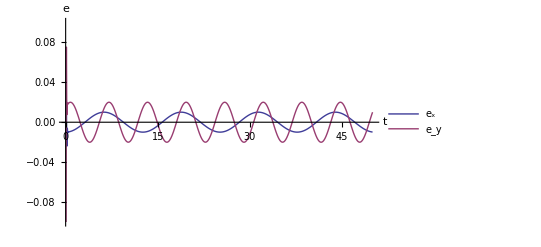

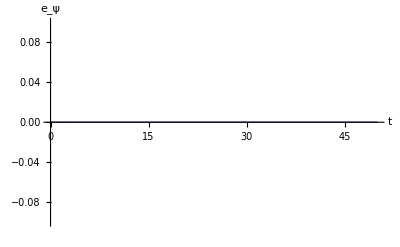

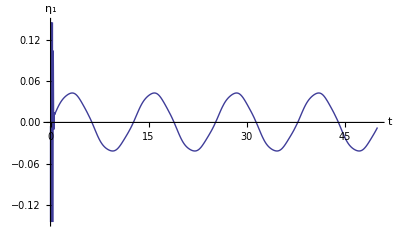

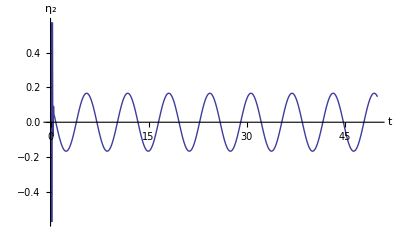

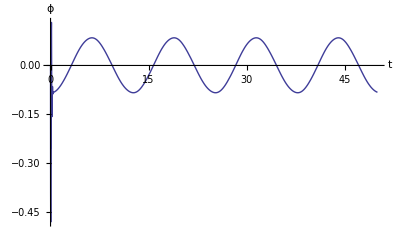

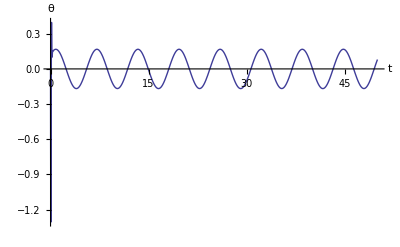

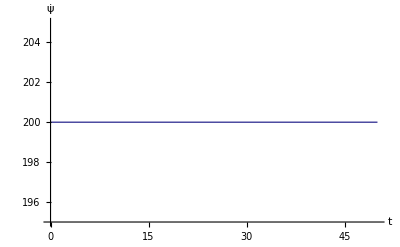

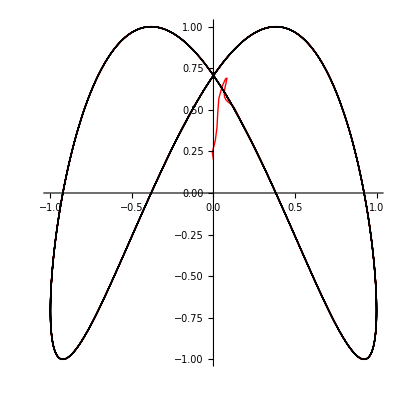

```mathematica
wirowanie = 200;
tmax =50;

q0={x[0]== 0, y[0]==0.2, Subscript[θ, 0][0]==0, ϕ[0]==0, θ[0]==0, ψ[0]==0};
k1=50;
k2=40;
w={x[t],y[t]};

For[i=0,i<1,i++,
Print[i];
Which[i==0,{xd[t_],yd[t_]}=osemka[t,1],i==1,{xd[t_],yd[t_]}=kolo[t,3,1],i==2,{xd[t_],yd[t_]}=liniaX[t,3,1],True,{xd[t_],yd[t_]}=kwadrat[t,3,5]];
wd={xd[t],yd[t],wirowanie};
M = wyliczSterowanie[wd,w,k1,k2];
rozwiazanie = rozwiazRownania[M,q0,tmax];
wyrysuj[rozwiazanie, tmax,False,i];
];
```

```mathematica
(*Export["C:\\Users\\Admin\\Documents\\GitHub\\hog\\prezentacja\\test.avi",anim,"FrameRate"->100];*)
```